## Geometry Computation

## Overview

Regions

Basic Regions

Formula Regions

Mesh Regions

Derived Regions

Region Properties

Dimension Properties

Membership Properties

Moment/Integration Properties

Distance/Optimization Properties

Region Solvers

Visualizing

Integrating

Optimizing

Solving Equations & Inequalities

Solving Partial Differential Equations

## Regions

### Preamble

A region ℛ⊆ℝ^n is a subset of ℝ^n. In the Wolfram Language, a region is an expression for which

```mathematica
RegionQ[expression]
```

returns True.

Built-in Regions

Simple and common

Specified with a few parameters

Example: Ball[c, r]

Formula Regions

Flexible, exact and powerful

Specified with formulas

Example: ImplicitRegion[x^2≤y,{x,y}]

Mesh Regions

Flexible, approximate and powerful

Specified with points and cells

Example: MeshRegion[{p_1,…,p_n},Tetrahedron[{vol_1,…,vol_m}]]

Derived Regions

Flexible and powerful

Specified with regions and additional information

Example: RegionUnion[ℛ_1,ℛ_2]

### Built-in Regions

#### 1D Regions

Point
-Graphics- | Lines
-Graphics- | Interval
-Graphics-

#### 2D Regions

Points
-Graphics- | Lines
-Graphics- | InfiniteLine
-Graphics- | HalfLine
-Graphics-
Triangle
-Graphics- | Rectangle
-Graphics- | Parallelogram
-Graphics- | Polygon
-Graphics-
RegularPolygon
-Graphics- | Circle
-Graphics- | Insphere
-Graphics- | Annulus
-Graphics-
Disk
-Graphics- | DiskSegment
-Graphics- | StadiumShape
-Graphics- | HalfPlane
-Graphics-
Hyperplane
-Graphics- | HalfSpace
-Graphics- | AffineHalfSpace
-Graphics- |

#### 3D Regions

Point
-Graphics3D- | Line
-Graphics3D- | InfiniteLine
-Graphics3D- | HalfLine
-Graphics3D-
Polygon
-Graphics3D- | Tetrahedron
-Graphics3D- | Pyramid
-Graphics3D- | Prism
-Graphics3D-
Cuboid
-Graphics3D- | Parallelepiped
-Graphics3D- | Cone
-Graphics3D- | SphericalShell
-Graphics3D-
Sphere
-Graphics3D- | Ellipsoid
-Graphics3D- | Cylinder
-Graphics3D- | CapsuleShape
-Graphics3D-
HalfPlane
-Graphics3D- | InfinitePlane
-Graphics3D- | Hyperplane
-Graphics3D- | HalfSpace
-Graphics3D-
AffineHalfSpace
-Graphics3D- | AffineSpace
-Graphics3D- |  |

#### nD Regions

```mathematica
Point
Line
InfiniteLine
HalfLine
Polygon
Simplex
Cuboid
Ball
Ellipsoid
SphericalShell
HalfPlane
InfinitePlane
Hyperplane
HalfSpace
AffineHalfSpace
AffineSpace
```

### Formula Regions

Formula regions are flexible and exact, and allow for general formula specification whether implicit or explicit.

ImplicitRegion[p[x],x] | Cell["ℛ = {x | p[x]}"]
ParametricRegion[f[u],u] | Cell["ℛ = {y | y = f[u]}"]

ImplicitRegion

```mathematica
ℛ=ImplicitRegion[1≤x^2+y^2≤2,{x,y}]
```

```mathematica
Region[ℛ,ImageSize->Small,FrameTicks->None]
```

```mathematica
Integrate[1,x∈ℛ]
```

```mathematica
ℛ=ImplicitRegion[x y z≤1,{{x,-5,5},{y,-5,5},{z,-5,5}}]
```

```mathematica
RegionPlot3D[ℛ,ImageSize->Small,PlotStyle->Opacity[0.5]]
```

```mathematica
Integrate[1,x∈ℛ]
```

ParametricRegion

```mathematica
ℛ=
[{Cos[θ],Sin[θ]},{{θ,0,2π}}]
```

```mathematica
Region[ℛ,ImageSize->Small]
```

```mathematica
constraint = -3/4+(5*x-20*x^3+16*x^5)^2-(5*x-20*x^3+16*x^5)*(1-8*y^2+8*y^4)+(1-8*y^2+8*y^4)^2≤ 0;
ℛ = ParametricRegion[{{x,x^2 +y^2}, constraint},{x,y}]
```

```mathematica
Region[ℛ,ImageSize->Small]
```

### Mesh Regions

#### Mesh regions

Mesh regions are flexible and approximate. Using piecewise linear cells can be used to approximate most regions.

MeshRegion[{p_1,p_2,…},{c_1,c_2,…}] | disjoint union of cells ℛ = ∪_i c_i (arbitrary dim regions in 1D/2D/3D)
BoundaryMeshRegion[{p_1,p_2,…},{bc_1,bc_2,…}] | region inside boundary (full dim regions in 1D/2D/3D)

```mathematica
ℛ=MeshRegion[{{0,0},{1,0},{0,1},{1,1}},Triangle[{{1,2,3},{3,2,4}}],MeshCellLabel->0->"Index",ImageSize->Small]
```

```mathematica
ℛ=MeshRegion[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}},{Tetrahedron[{{1,2,3,5},{1,3,4,5}}]},MeshCellLabel->0->"Index",ImageSize->Small]
```

```mathematica
ℛ=BoundaryMeshRegion[{{0,0},{3,0},{3,3},{0,3},{1,1},{2,1},{2,2},{1,2}},Line[{1,2,3,4,1}],Line[{5,6,7,8,5}],MeshCellLabel->0->"Index",ImageSize->Small]
```

#### Mesh based regions

Typically mesh based regions are automatically constructed.

DelaunayMesh[{p_1,p_2,…}] | Delaunay mesh from points
VoronoiMesh[{p_1,p_2,…}] | Voronoi mesh from points
ConvexHullMesh[{p_1,p_2,…}] | convex hull boundary mesh from points
DiscretizeGraphics[g] | fully discretize 2D/3D graphics
BoundaryDiscretizeGraphics[g] | boundary discretize 2D/3D graphics
DiscretizeRegion[ℛ] | fully discretize 1D/2D/3D regions
BoundaryDiscretizeRegion[ℛ] | boundary discretize 1D/2D/3D regions
TriangulateMesh[ℳℛ] | fully triangulate mesh from boundary mesh
BoundaryMesh[ℳℛ] | boundary mesh from full mesh
HighlightMesh[ℳℛ,…] | style and label mesh cells

DelaunayMesh

```mathematica
DelaunayMesh[RandomReal[{0,1},{25,3}]]
```

VoronoiMesh

```mathematica
points=RandomReal[{0,1},{25,2}];
```

```mathematica
Show[VoronoiMesh[points],Graphics[{Orange,Point[points]}]]
```

Discretizing a graphics


```mathematica
BoundaryDiscretizeGraphics[-Graphics-]
```

```mathematica
TriangulateMesh[%]
```

```mathematica
MeshCellCount[%]
```

Discretizing a region

```mathematica
ℳ=BoundaryDiscretizeRegion[ImplicitRegion[-1+(-1+18 x^2-48 x^4+32 x^6)^2+(-1+18 y^2-48 y^4+32 y^6)^2 ≤0,{x,y}],MaxCellMeasure->0.01]
```

```mathematica
HighlightMesh[ℳ,Style[{1,All},Red]]
```

### Derived Regions

Derived regions, are constructed from other regions.

RegionUnion[ℛ_1,ℛ_2] | ℛ = {x | x ∈ ℛ_1 ∨ x ∈ ℛ_2} = ℛ_1 ∪ ℛ_2
RegionIntersection[ℛ_1,ℛ_2] | ℛ = {x | x ∈ ℛ_1 ∧ x ∈ ℛ_2} = ℛ_1 ∩ ℛ_2
RegionDifference[ℛ_1,ℛ_2] | ℛ = {x | x ∈ ℛ_1 ∧ x ∉ ℛ_2} = ℛ_1 \ ℛ_2
RegionSymmetricDifference[ℛ_1,ℛ_2] | ℛ = {x | x ∈ ℛ_1 ⊻ x ∉ ℛ_2} = ℛ_1 Δ ℛ_2
BooleanRegion[f,{ℛ_1,ℛ_2,…}] | ℛ = {x | f[x ∈ ℛ_1,x ∈ ℛ_2,…]} 
RegionProduct[ℛ_1,ℛ_2,…] | ℛ = {{x_1,x_2,…} | x_1 ∈ ℛ_1 ∧ x_2 ∈ ℛ_2 ∧ ⋯} = ℛ_1 × ℛ_2 × ⋯
TransformedRegion[ℛ_1,f] | ℛ = {f[x] | x ∈ ℛ_1 } = f[ℛ_1]
InverseTransformedRegion[ℛ_1,f] | ℛ = {x | f[x] ∈ ℛ_1 } = f^-1[ℛ_1]
RegionBoundary[ℛ_1] | ℛ = {x | x ∈ ∂ℛ_1 } = ∂ℛ_1

```mathematica
r1=Disk[{-1/2,0}];
r2=Disk[{1/2,0}];
```

```mathematica
d1=RegionUnion[r1,r2];
d2=RegionIntersection[r1,r2];
d3=RegionDifference[r1,r2];
d4=RegionSymmetricDifference[r1,r2];
```

```mathematica
Table[Show[BoundaryDiscretizeRegion[r],PlotRange->{{-1.65,1.65},{-1.1,1.1}},PlotLabel->Head[r]],{r,{d1,d2,d3,d4}}]
```

```mathematica
ℛ=DiscretizeGraphics[Cuboid[]]
```

```mathematica
t1=ScalingTransform[{2,1,1}];
t2=RotationTransform[π/3,{1,1,1}];
t3=ShearingTransform[π/6,{1,1,0},{0,0,1}];
t4=Composition[t3,t2,t1];
```

```mathematica
Table[TransformedRegion[ℛ,t],{t,{t1,t2,t3,t4}}]
```

## Region Properties

### Preamble

Region properties summarize some aspect of regions.

Dimension Properties

RegionEmbeddingDimension

RegionDimension

Membership Properties

x∈ℛ

RegionMember, RegionMemberFunction

Moment/Integration Properties

ArcLength, Area, Volume, RegionMeasure

RegionCentroid

Distance/Optimization Properties

RegionNearest, RegionNearestFunction

RegionDistance, RegionDistanceFunction

RegionSignedDistance, RegionDistanceFunction

### Dimension Properties

RegionDimension[ℛ] | dimension of region
RegionEmbeddingDimension[ℛ] | dimension of embedding space

```mathematica
{{"", 0, 1, 2, 3}, {2, -Graphics-, -Graphics-, -Graphics-, ""}, {3, -Graphics3D-, -Graphics3D-, -Graphics3D-, -Graphics3D-}}//CellDisplay
```

| 0 | 1 | 2 | 3
2 | -Graphics- | -Graphics- | -Graphics- | 
3 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

#### RegionEmbeddingDimension

```mathematica
RegionEmbeddingDimension[Disk[]]
```

```mathematica
RegionEmbeddingDimension[Circle[]]
```

```mathematica
RegionEmbeddingDimension[Point[{1,2,3,4}]]
```

#### RegionDimension

```mathematica
RegionDimension[Disk[]]
```

```mathematica
RegionDimension[Circle[]]
```

```mathematica
RegionDimension[Point[{1,2,3,4}]]
```

### Membership Properties

```mathematica
Grid[{{"Element[x,ℛ]","assert that x∈ℛ"},
{HoldForm[RegionMember[ℛ,x]],"find conditions for Cell["x∈ℛ",ExpressionUUID->"ee16ccb3-ed15-4afa-bf21-b8acdf9a93db"]"},
{HoldForm[RegionMember[ℛ]],"find region member function"}},BaseStyle->"Text",Alignment->Left]//FramedStatement
```

Element[x,ℛ] | assert that x∈ℛ
RegionMember[ℛ,x] | find conditions for Cell["x∈ℛ"]
RegionMember[ℛ] | find region member function

Element

Assert membership.

```mathematica
{x,y}∈Disk[{0,0},r]
```

```mathematica
Integrate[1,%]
```

RegionMember

Find conditions for membership.

```mathematica
RegionMember[Disk[{0,0},r],{x,y}]
```

RegionMemberFunction

Get a member function.

```mathematica
mf=RegionMember[Disk[{0,0},1]]
```

RegionMemberFunction[…]

```mathematica
mf[{1/2,0}]
```

True

```mathematica
ℛ=ConvexHullMesh[RandomReal[1,{200,3}]];
pts=RandomReal[1,{10^5,3}];
cls=RegionMember[ℛ,pts];
```

```mathematica
Graphics3D[{PointSize[Tiny],{Green,Point@Pick[pts,cls,True]},{Red,Point@Pick[pts,cls,False]}}]
```

-Graphics3D-

### Moment/Integration Properties

ArcLength[ℛ] | curve length for 1D region
Area[ℛ] | surface area for 2D region
Volume[ℛ] | solid volume for 3D region
RegionMeasure[ℛ] | count, length, area, volume etc (∫_(x∈ℛ) 1)
RegionCentroid[ℛ] | centrality measure ((∫_(x∈ℛ) x)/m)

#### RegionMeasure

```mathematica
ArcLength[Circle[]]
```

```mathematica
ArcLength[ImplicitRegion[x^2+(y/2)^2==1,{x,y}]]
```

```mathematica
Area[Disk[]]
```

```mathematica
Area[-Graphics-]
```

```mathematica
Volume[Ball[]]
```

```mathematica
Volume[-Graphics3D-]
```

```mathematica
Table[RegionMeasure[Sphere[n]],{n,1,10}]
```

```mathematica
FindSequenceFunction[%,n]//FullSimplify
```

#### RegionCentroid

```mathematica
RegionCentroid[Disk[{x,y},r]]
```

```mathematica
RegionCentroid[Polygon[{{0,0},{3,-1},{1,0},{3,1}}]]
```

```mathematica
Graphics[{LightBlue,Polygon[{{0,0},{3,-1},{1,0},{3,1}}],Red,Point[%]}]
```

```mathematica
RegionCentroid[-Graphics3D-]
```

### Distance/Optimization Properties

RegionNearest[ℛ,p] | nearest point in region
RegionDistance[ℛ,p] | minimum distance to region
SignedRegionDistance[ℛ,p] | distance to region or negative distance to complement

#### RegionNearest

Gives the nearest point in a region.

```mathematica
RegionNearest[Disk[],{x,y}]
```

Piecewise[{{{x,y}, √(x^2+y^2)≤1}, {{x/(√(x^2+y^2)),y/(√(x^2+y^2))}, True}}]

```mathematica
RegionNearest[Triangle[{{0,0},{1,0},{0,1}}],{x,y}]
```

Piecewise[{{{x,y}, y≥0&&1-x-y≥0&&x≥0}, {{x,0}, y<0&&x≥0&&-1+x≤0}, {{x+1/2 (1-x-y),1/2 (1-x-y)+y}, 1-x-y<0&&1-x+y≥0&&-1-x+y≤0}, {{0,y}, x<0&&1-y≥0&&-y≤0}, {{0,0}, -y>0&&x<0}, {{1,0}, -1+x>0&&1-x+y<0}, {{0,1}, True}}]

```mathematica
rnf=RegionNearest[Triangle[{{0,0},{1,0},{0,1}}]]
```

RegionNearestFunction[…]

```mathematica
rnf/@{{2,2},{1,0},{3,4}}
```

{{1/2,1/2},{1,0},{0,1}}

```mathematica
Show[{Region[Triangle[{{0,0},{1,0},{0,1}}]],Graphics[Point[{{2,2},{1,0},{3,4},{1/2,1/2},{1,0},{0,1}}]]}];
```

#### RegionDistance

Gives the distance to the nearest point in a region.

```mathematica
dtri=RegionDistance[Triangle[{{0,0},{1,0},{0,1}}]]
```

```mathematica
ContourPlot[dtri[{x,y}],{x,-2,3},{y,-2,3},Contours->{0.25,0.5,1.0},Exclusions->None]
```

```mathematica
dtet=RegionDistance[Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,1.}}]]
```

```mathematica
ContourPlot3D[dtet[{x,y,z}],{x,-2,3},{y,-2,3},{z,-2,3},Mesh->None,Contours->{0.25,0.5,1.0},PlotPoints->50,MaxRecursion->0,ContourStyle->ColorData[95,"ColorList"],BaseStyle->Opacity[0.5],ImageSize->Small]
```

## Region Solvers

### Preamble

Region solvers use a flexible problem language that can accept and is optimized for region arguments.

Visualize over a region

Plot • ParametricPlot • Plot3D • ParametricPlot3D • DensityPlot • ContourPlot • VectorPlot • StreamPlot • VectorDensityPlot • StreamDensityPlot • NumberLinePlot • RegionPlot • RegionPlot3D

Integrate over a Region

Integrate • NIntegrate

Solve PDEs over a Region

NDSolve • NDSolveValue • ParametricNDSolve • ParametricNDSolveValue

Optimize with Region Constraints

Minimize • MinValue • ArgMin • Maximize • MaxValue • ArgMax • NMinimize • NMinValue • NArgMin • NMaximize • NMaxValue • NArgMax • FindMinimum • FindMinValue • FindArgMin • FindMaximum • FindMaxValue • FindArgMax

Solve Equations with Region Constraints

Solve • NSolve • Reduce • FindInstance • Resolve

### Visualize over a Region

Plot[…,x∈ℛ]
ParametricPlot[…,{u,v}∈ℛ]
Plot3D[…,{x,y}∈ℛ]
⋮
VectorPlot[…,{x,y}∈ℛ]
StreamPlot[…,{x,y}∈ℛ]
⋮

```mathematica
ℛ=Interval@@Table[{k π-π/2,(k+1)π-π/2},{k,2,10,2}]
```

```mathematica
Plot[Sin[x],x∈ℛ]
```

```mathematica
Plot3D[Sin[2π x y],{x,y}∈Disk[]]
```

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,y}∈Disk[{0,0},3]]
```

### Integrate over a Region

Integrate[f[x], x∈ℛ]    (∫_(x∈ℛ) f[x])
NIntegrate[f[x],x∈ℛ]

```mathematica
Integrate[1,{x,y}∈Circle[{1,2},r]]
```

```mathematica
Integrate[1,{x,y}∈Disk[]]
```

```mathematica
Integrate[1,{x,y,z}∈Ball[]]
```

```mathematica
NIntegrate[1,{x,y,z}∈-Graphics3D-]
```

```mathematica
NIntegrate[1,{x,y,z}∈-Graphics3D-]
```

```mathematica
NIntegrate[1,{x,y,z}∈-Graphics3D-]
```

### Solve PDEs over a Region

NDSolve[…,…,{x_1,…}∈ℛ]
NDSolveValue[…,…,{x_1,…}∈ℛ]

```mathematica
usol=NDSolveValue[{∇_{x,y}^2 u[x,y]==1,DirichletCondition[u[x,y]==0,True]},u,{x,y}∈Disk[]]
```

InterpolatingFunction[{{-1., 1.}, {-1., 1.}}, <>]

```mathematica
Plot3D[usol[x,y],{x,y}∈Disk[]]
```

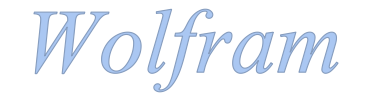
```mathematica
ℛ=-Graphics-;
```

```mathematica
usol=NDSolveValue[{∇_{x,y}^2 u[x,y]==10,DirichletCondition[u[x,y]==0,True]},u,{x,y}∈ℛ]
```

```mathematica
Plot3D[usol[x,y],{x,y}∈ℛ,PlotPoints->150,ImageSize->550,PlotRange->{All,All,{All,-2}},Mesh->None,BoxRatios->{1,0.273,0.4},PlotTheme->"Marketing",PlotStyle->Opacity[0.5]]
```

### Optimize with Region Constraints

Minimize[{f[x],…},x∈ℛ]
⋮
NMinimize[{f[x],…},x∈ℛ]
⋮
FindMinimum[{f[x],…},x∈ℛ]
⋮

```mathematica
pmin=ArgMin[x^2-x y+y^2,{x,y}∈Disk[]]
```

```mathematica
pmax=ArgMax[x^2-x y+y^2,{x,y}∈Disk[]]
```

```mathematica
Legended[Show[ContourPlot[x^2-x y+y^2,{x,y}∈Disk[]],Graphics[{PointSize[Medium],{Red,Point[pmin]},{Blue,Point[pmax]}}]],SwatchLegend[{Red,Blue},{"min","max"}]]
```

```mathematica
ℛ1=Disk[];
ℛ2=Rectangle[{2,1},{3,3}];
```

```mathematica
{p1t,p2t}=NArgMin[EuclideanDistance[p1,p2],{p1∈ℛ1,p2∈ℛ2}]
```

```mathematica
{q1t,q2t}=NArgMax[EuclideanDistance[p1,p2],{p1∈ℛ1,p2∈ℛ2}]
```

```mathematica
Graphics[{{LightBlue,ℛ1,ℛ2},{Dashed,Line[{p1t,p2t}],Red,Point[{p1t,p2t}]},{Dashed,Line[{q1t,q2t}],Red,Point[{q1t,q2t}]}}]
```

### Solve Equations with Region Constraints

Solve[…,x∈ℛ]
NSolve[…,x∈ℛ]
Reduce[…,x∈ℛ]
FindInstance[…,x∈ℛ]
Resolve[∃_y y∈𝒮&&⋯,x∈ℛ]
⋮

```mathematica
line1=InfiniteLine[{0,0},{1,1}];
line2=InfiniteLine[{{0,1},{1,0}}];
```

```mathematica
sol=NSolve[{x,y}∈line1∧{x,y}∈line2,{x,y}]
```

```mathematica
Graphics[{{Lighter[Blue,0.5],line1,line2},{Red,Point[{x,y}/.sol]}},Axes->True]
```

```mathematica
line=InfiniteLine[{0,0},{1,1}];
circle=Circle[{0,0},1];
```

```mathematica
sol=Solve[p∈line∧p∈circle,p]
```

```mathematica
Graphics[{{Lighter[Blue,0.5],line,circle},{Red,Point[p/.sol]}},Axes->True]
```

```mathematica
{s1,s2,s3}=Table[Sphere[{1/3 Cos[k 2π/3],1/3 Sin[k 2π/3],0}],{k,0,2}];
```

```mathematica
sol=Solve[p∈s1∧p∈s2∧p∈s3,p]
```

```mathematica
Graphics3D[{{Opacity[0.5],s1,s2,s3},{Red,PointSize[Large],Point[p/.sol]}}]
```

## Applications & Explorations

### Hausdorff Distance d_H[𝒜,ℬ]

The Hausdorff distance d_H[𝒜,ℬ]=Max[h[𝒜,ℬ],h[ℬ,𝒜]] where h[𝒜,ℬ] is the directed Hausdorff distance from region 𝒜 to ℬ given by h(𝒜,ℬ)==sup_(q∈ℬ) inf_(p∈𝒜) d(p,q).

```mathematica
{-Graphics-,-Graphics-}
```

Lets start with two simple regions:

```mathematica
𝒜=Triangle[{{0,0},{2,0},{0,1}}];
ℬ=Triangle[{{0,0},{1,0},{0,3/2}}];
```

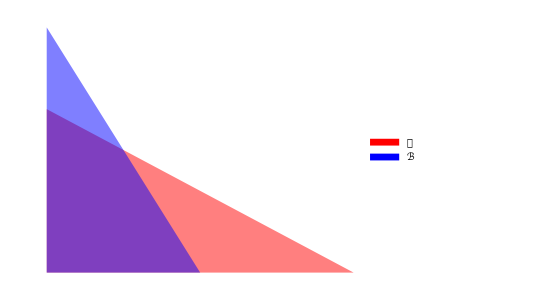

```mathematica
Legended[Graphics[{Opacity[0.5],{Red, 𝒜},{Blue,ℬ}}],SwatchLegend[{Red,Blue},{"𝒜","ℬ"}]]
```

The directed Hausdorff distance from 𝒜 to ℬ is h(𝒜,ℬ)==sup_(q∈ℬ) inf_(p∈𝒜) d(p,q):

```mathematica
d1=RegionDistance[𝒜,{x,y}]
```

As expected the distance is zero where ℬ overlaps with 𝒜:

```mathematica
Plot3D[d1,{x,y}∈ℬ,PlotRange->All]
```

This is h[𝒜,ℬ]:

```mathematica
hAB=MaxValue[d1,{x,y}∈ℬ]
```

If h[𝒜,ℬ]==ϵ then we can conclude ℬ^cl⊆𝒜_ϵ^cl where 𝒜_ϵ={x|d[𝒜,x]≤ϵ}:

```mathematica
Show[RegionPlot[d1≤hAB,{x,-1,3},{y,-1,5/2}],Graphics[{Opacity[0.5],{Red, 𝒜},{Blue,ℬ}}]]
```

And we get h[ℬ,𝒜] similarly as well as d_H[𝒜,ℬ]

```mathematica
hBA=MaxValue[RegionDistance[ℬ,{x,y}],{x,y}∈𝒜]
```

```mathematica
dH=Max[hAB,hBA]
```

### Cantor Sets

The Cantor set 𝒜 is defined recursively with 𝒜_0=[0,1] and 𝒜_n=∪_([a,b]∈𝒜_(n-1))([a,(b-a)/3]∪[a+(b-a)2/3,b]):

```mathematica
cantorRules={a_,b_}:>{{a,a+(b-a)/3},{a+(b-a)2/3,b}};
```

```mathematica
CantorRegion[n_Integer?NonNegative]:=
Interval@@Nest[Flatten[Map[Function[s,s/.cantorRules],#],1]&,{{0,1}},n]
```

```mathematica
CantorRegion[0]
```

```mathematica
CantorRegion[1]
```

```mathematica
NumberLinePlot[Table[CantorRegion[i],{i,3}],{x,0,1}]
```

The measure, i.e. length, evolves in an interesting way:

```mathematica
Table[{i,RegionMeasure[CantorRegion[i]]},{i,5}]
```

```mathematica
FindSequenceFunction[%,k]
```

Cantor dust in ℝ^d is defined as the product of d Cantor sets: 𝒟_n=𝒜_n×⋯×𝒜_n:

```mathematica
CantorDust[n_Integer,d_]:=Module[{An},
An=DiscretizeRegion[CantorRegion[n],MaxCellMeasure->∞];
RegionProduct@@Table[An,{d}]
]
```

```mathematica
Table[CantorDust[k,2],{k,3}]
```

```mathematica
Table[CantorDust[k,3],{k,3}]
```

See how the measure evolves for these regions:

```mathematica
Table[{k,RegionMeasure@CantorDust[k,2]},{k,5}]//Rationalize
```

```mathematica
FindSequenceFunction[%,k]
```

```mathematica
Table[{k,RegionMeasure@CantorDust[k,3]},{k,0,3}]//Rationalize
```

```mathematica
FindSequenceFunction[%,k]
```

Generalize the Cantor dust definition to 𝒟_(k_1,…,k_d)=𝒜_k_1×⋯×𝒜_k_d:

```mathematica
CantorDust[n_List]:=
RegionProduct@@Table[DiscretizeRegion[CantorRegion[n⟦i⟧],MaxCellMeasure->∞],{i,Length[n]}]
```

```mathematica
CantorDust[{2,3,1}]
```

### Seidel’s Polyhedron

The Seidel polyhedron is a cuboid with tunnels in every direction that never cross. We will build this directly using MeshRegion.

-Graphics3D-

The idea is build a grid of cuboid cells and decide which ones to keep. The construction will work for any other region that can be built similarly. We will need a utility that predicts how a position {i_1,i_2,i_3} in a dimension {d_1,d_2,d_3} array transforms into a position j when flattened. The basic formula is given by j=1+(i_3-1)+d_3(i_2-1)+d_3 d_2(i_1-1):

```mathematica
IndexFlatten[i_List,d_List]:=1+FoldList[Times,1,Most[Reverse[d]]].Reverse[(i-1)]
```

```mathematica
IndexFlatten[{Subscript[i, 1],Subscript[i, 2],Subscript[i, 3]},{Subscript[d, 1],Subscript[d, 2],Subscript[d, 3]}]
```

```mathematica
Extract[Array[a,{2,3,4}],{1,3,2}]
```

```mathematica
Extract[Flatten[Array[a,{2,3,4}]],IndexFlatten[{1,3,2},{2,3,4}]]
```

Now we can build the MeshRegion corresponding to any array:

```mathematica
ArrayGridMesh[a_List]/;ArrayQ[a]&&ArrayDepth[a]==3:=
Module[{m,n,p,pa,ia,re},
{m,n,p}=Dimensions[a];
pa=Table[{x,y,z},{x,0,m},{y,0,n},{z,0,p}];
re={{1,1,1},{2,1,1},{2,2,1},{1,2,1},{1,1,2},{2,1,2},{2,2,2},{1,2,2}};
ia=Table[IndexFlatten[#,{m,n,p}+1]&/@TranslationTransform[ind-1][re],{ind,Position[a,1]}];
MeshRegion[Flatten[pa,2],Hexahedron[ia]]
]
```

We can use this to convert any array to a MeshRegion ...

```mathematica
ArrayGridMesh[{{{1,1,1},{1,0,1},{1,1,1}},
{{1,1,1},{1,0,1},{1,1,1}},{{1,1,1},{1,0,1},{1,1,1}}}]
```

```mathematica
ArrayGridMesh[CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},10]]
```

Defining Seidel’s polyhedron is then about defining the right array. Some experimentation gives something reasonably simple:

```mathematica
SeidelMesh[{r_,s_,t_}]:=
ArrayGridMesh[Table[If[Mod[i,4]==2&&Mod[j,4]==2||Mod[i,4]==0&&Mod[k,4]==0||Mod[j,4]==0&&Mod[k,4]==2,0,1],{i,3+r 4},{j,3+s 4},{k,3+t 4}]]
```

```mathematica
SeidelMesh[{1,1,1}]
```

By converting to BoundaryMeshRegion and controlling some styling we have the desired result:

```mathematica
HighlightMesh[BoundaryMesh@SeidelMesh[{2,2,2}],{Style[1,None],Style[2,Opacity[0.5]]}]
```

```mathematica
HighlightMesh[BoundaryMesh@SeidelMesh[{4,4,4}],{Style[1,None],Style[2,Opacity[0.5]]}]
```

### RegionNearest and Voronoi Diagrams

A Voronoi diagram for points {p_1,…,p_n} is a mesh region with a cell c_i for each point p_i indicating the region of points that are closer to p_i than any other point. Specifically we have c_i=∧_(j=1,j≠i)^n d(p_i,p)≤d(p_j,p):

```mathematica
pts={{1,1},{1,2},{3,1},{4,4}};
```

```mathematica
Show[VoronoiMesh[pts,{{-1,5},{-1,5}}],Graphics[{PointSize[Large],Point[pts]}]]
```

Or compute the cells directly through  c_i=∧_(j=1,j≠i)^n d(p_i,p)≤d(p_j,p):

```mathematica
n=Length[pts];
cells=And@@@Table[EuclideanDistance[pts⟦i⟧,{x,y}]≤EuclideanDistance[pts⟦j⟧,{x,y}],{i,n},{j,Complement[Range[n],{i}]}];
```

```mathematica
Show[RegionPlot[cells,{x,-1,5},{y,-1,5}],Graphics[{PointSize[Large],Point[pts]}]]
```

This means that we can cheaply compute RegionNearest with this data structure, since for each cell c_i we have a trivial nearest projection function π_i[p]=p_i. RegionNearest in effect has to compute these types cells for points, but also for general regions.

```mathematica
PiecewiseValuesConditions[pw_Piecewise,simp_:Simplify]:=
Module[{vals,conds},
{vals,conds}=Transpose@First@pw;
vals=Append[vals,Last[pw]];
conds=Append[conds,simp[And@@(Not/@conds)]];
{vals,conds}
];
```

```mathematica
RegionNearest[Point[pts],{x,y}]
```

```mathematica
{vals,conds}=PiecewiseValuesConditions[%];
```

```mathematica
RegionPlot[conds,{x,-1,5},{y,-1,5}]
```

For a more general region it gets more complicated, because we get new cells to accommodate more projection functions:

```mathematica
RegionNearest[Triangle[],{x,y}]
```

```mathematica
{vals,conds}=PiecewiseValuesConditions[%];
```

```mathematica
RegionPlot[conds,{x,-1,2},{y,-1,2}]
```

For a standard tetrahedron:

```mathematica
Graphics3D[Tetrahedron[]]
```

```mathematica
RegionNearest[Tetrahedron[],{x,y,z}]
```

If we plot the generalized Voronoi cells for the tetrahedron we get:

-Graphics3D-